### Figure

-Graphics-

Find the Force versus Displacement curve.
In particular, find the maximum force that can be applied on the two bars.

### Background

σ = P/A      		ϵ = δ/L

P = EA/L δ

Yielding occurs when σ = σ_Y

σ_Y = P_Y/A    ⇒   P_Y = σ_Y A

### Calculations

```mathematica
UnitConvert[ Quantity[200., "Giga" "Pascals"]*Quantity[2*10^-4, ("Meters")^2], "Mega" "Newtons"]
```

40. M N

```mathematica
UnitConvert[ Quantity[50., "Mega" "Pascals"]*Quantity[2*10^-4, ("Meters")^2], "Mega" "Newtons"]
```

### Notes

#### Preliminary

EA_Green/L = 40 MN/m,  EA_Red/L = 20MN/m

This means that every 1 m extension, we get 40 MN in the green and 20 MN in the red of force resisting.

When does yielding occur?

σ_(Y of Green) A_Green = 0.01 MN,   σ_(Y of Red) A_Red = 0.02 MN

So while the green bar resists faster (stiffer), the red bar is stronger.

#### Incremental method

Green bar yields first.  When does that occur?

The load increases, the stiffness is that of both bars combined (add them) until green bar yields.  At that point, the green bar resists with a constant force of 0.01 MN, no matter how much more deflection occurs.  Beyond that point, only the red bar increases its resistance until it too yields.  At that point, we’ve reached maximum resistance and beyond that is failure.

After the green bar yields, the red bar is still behaving elastically.  When does the red bar yield?

EA_Green/L = 40 MN/m,  EA_Red/L = 20MN/m
This means that every 1 m extension, we get 40 MN in the green and 20 MN in the red of force resisting.

```mathematica
Papplied[δ_] := Piecewise[{{60 * δ, 0<= δ<= 0.00025}, {0.01 + 20 * δ, 0.00025 <= δ <= 0.001}, {0.01 + 0.02, True}}]
```

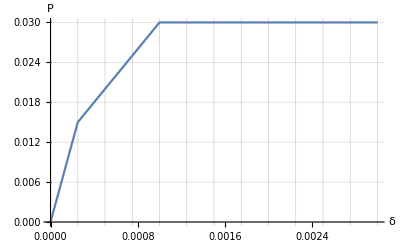

```mathematica
Plot[ Papplied[δ], {δ, 0, 0.003}, PlotRange -> All,
AxesLabel->(Style[#, Large]& /@ {"δ", "P"}),
GridLines -> {Range[0, 0.003, 0.00025], Automatic}]
```

The final force-deflection is then as follows:

In the green bar, the force developed is 40 × δ  until green yields
In the red bar, the force developed is 20 × δ  until red yields

When does yielding occur in each bar?
σ_(Y of Green) A_Green = 0.01 MN,   σ_(Y of Red) A_Red = 0.02 MN

```mathematica
Solve[ 40 δ == 0.01, δ]
```

{{δ→0.00025}}

```mathematica
Solve[ 20 δ == 0.02, δ]
```

{{δ→0.001}}

#### Equilibrium method

What is the maximum force that can be resisted by the 2 bars?

When does yielding occur?

σ_(Y of Green) A_Green = 0.01 MN,   σ_(Y of Red) A_Red = 0.02 MN

P_(ultimate of 2 bar system) = σ_(Y of Green) A_Green + σ_(Y of Red) A_Red

P_(ultimate of 2 bar system) = 0.01MN + 0.02 MN = 0.03 MN = 30 kN

#### Kinetic method

We use the principle of virtual work and we postulate a failure mechanism.